```mathematica
dir = NotebookDirectory[]
```

/Users/nico/Documents/projects/cell_colonies/embryonic_stem_cells/software/

```mathematica
data = Import[dir<>"data.m"];
```

```mathematica
First/@data
```

{Divisions2i,DivisionsLif,Measurements2i,MeasurementsLif}

```mathematica
tdivs = ("Divisions2i"/.data)[[1]];
```

```mathematica
res =( "Measurements2i"/.data)[[1]];
```

```mathematica
scheme="CandyColors"
```

CandyColors

```mathematica
ids=Map[First,res,{2}];
```

```mathematica
todraw=Union@Flatten[ids];
```

```mathematica
rules = Last/@tdivs
```

{393217→393218,393217→393219,1310721→1310722,1310721→1310723,1048577→1048578,1048577→1048579,1900545→1900546,1900545→1900547,524289→524290,524289→524291,2555905→2555906,2555905→2555907,65537→65538,65537→65539,196609→196610,196609→196611,2359297→2359298,2359297→2359299,393218→393220,393218→393221,720897→720898,720897→720899,2359298→2359300,2359298→2359301,2293761→2293762,2293761→2293763,1572865→1572866,1572865→1572867}

```mathematica
cleanrules = rules;
```

```mathematica
g=Graph[rules/.Rule[x_,y_]->UndirectedEdge[x,y],EdgeStyle->Directive[Darker@ColorData["CandyColors",0.15]],VertexSize->0.75,VertexStyle->Directive[Large,ColorData["CandyColors",0.15]]]
```

-Graphics-

```mathematica
Clear[splitComponent]
splitComponent[{}]:={};
splitComponent[x_/;FreeQ[x,Alternatives[Sequence@@(First/@cleanrules)]]]:=x;
splitComponent[x_]:=Module[
{root,branches},
root=Select[x,MemberQ[First/@cleanrules,#]&&!MemberQ[Last/@Select[cleanrules,Function[z,MemberQ[x,z[[1]]]&&MemberQ[x,z[[2]]]]],#]&];
branches=ConnectedComponents[Evaluate[Subgraph[g,Complement[x,root]]]];
{root,splitComponent/@branches}
]
```

```mathematica
clones=ConnectedComponents[g]
```

{{393217,393218,393219,393220,393221},{1310721,1310722,1310723},{1048577,1048578,1048579},{1900545,1900546,1900547},{524289,524290,524291},{2555905,2555906,2555907},{65537,65538,65539},{196609,196610,196611},{2359297,2359298,2359299,2359300,2359301},{720897,720898,720899},{2293761,2293762,2293763},{1572865,1572866,1572867}}

```mathematica
todraw=First/@Select[Tally[Sort[Flatten[ids]]],Last[#]>2&]
```

{65537,65538,65539,131073,196609,196610,196611,262145,327681,393217,393218,393219,393220,393221,524289,524290,524291,655361,720897,720898,720899,786433,851969,983041,1048577,1048578,1048579,1114113,1179649,1245185,1310721,1310722,1310723,1507329,1572865,1572866,1572867,1638401,1703937,1769473,1835009,1900545,1900546,1900547,1966081,2031617,2097153,2162689,2293761,2293762,2293763,2359297,2359298,2359299,2359300,2359301,2424833,2490369,2555905,2555906,2555907,2686977,2752513,2818049,2883585,2949121,3014657,3080193,4063233,4128769,5701633,5898241,6619137,7405569,8257537,8978433,9240577,9830401,10027009,10354689,11206657,11599873,13434881,14024705,15728641,15990785,16187393,16449537,18284545,19464193,19660801,20316161,22020097,23003137,25231361,25427969,26214401,27590657,30539777,32571393,33816577,35323905,35717121}

```mathematica
clones=Join[ConnectedComponents[g],List/@Complement[Union[todraw],Flatten[clones]]];
```

```mathematica
clones2=Flatten[splitComponent[#]]&/@clones;
```

```mathematica
clones=clones2;
```

```mathematica
clones
```

{{393217,393218,393220,393221,393219},{1310721,1310722,1310723},{1048577,1048578,1048579},{1900545,1900546,1900547},{524289,524290,524291},{2555905,2555906,2555907},{65537,65538,65539},{196609,196610,196611},{2359297,2359298,2359300,2359301,2359299},{720897,720898,720899},{2293761,2293762,2293763},{1572865,1572866,1572867},{131073},{262145},{327681},{655361},{786433},{851969},{983041},{1114113},{1179649},{1245185},{1507329},{1638401},{1703937},{1769473},{1835009},{1966081},{2031617},{2097153},{2162689},{2424833},{2490369},{2686977},{2752513},{2818049},{2883585},{2949121},{3014657},{3080193},{4063233},{4128769},{5701633},{5898241},{6619137},{7405569},{8257537},{8978433},{9240577},{9830401},{10027009},{10354689},{11206657},{11599873},{13434881},{14024705},{15728641},{15990785},{16187393},{16449537},{18284545},{19464193},{19660801},{20316161},{22020097},{23003137},{25231361},{25427969},{26214401},{27590657},{30539777},{32571393},{33816577},{35323905},{35717121}}

```mathematica
drawt=Table[SortBy[Select[First/@res[[i]],MemberQ[todraw,#]&],Position[clones,#]&],{i,1,Length[res]}];
```

```mathematica
(*Clear[getSplitPoints]
getSplitPoints[object_,split_,int_,nobjs_]:=Module[
{daughters,areas,span,pts},
daughters= If[MemberQ[First/@split,object],Select[split,First[#]==object&],{}];
areas=If[daughters==={},{},First/@(Rest[daughters[[1]]]/.nobjs)];
span=Abs[Subtract@@Reverse[int]];
pts=(First[int]+# span)&/@N[(#/(Plus@@areas))&/@areas];
pts=Partition[Accumulate[Prepend[pts,int[[1]]]],2,1];
If[pts==={},{int},pts]
]*)
Clear[getSplitPoints]
getSplitPoints[object_,split_,int_,nobjs_]:=Module[
{daughters,areas,span,pts},
daughters= If[MemberQ[First/@split,object],Select[split,First[#]==object&],{}];
areas=If[daughters==={},{},First/@(Rest[daughters[[1]]]/.nobjs)];
span=Abs[Subtract@@Reverse[int]];
(*pts=(First[int]+# span)&/@N[(#/(Total[areas]))&/@Flatten[areas]];*)
pts=span*N[(#/(Total[areas]))]&/@Flatten[areas];
pts=Partition[Accumulate[Prepend[pts,int[[1]]]],2,1];
If[pts==={},{int},pts]
]
```

```mathematica
Clear[selectNextInterval]
selectNextInterval[id_,split_,nintv2_]:=Module[{hit,daughters,divided},
hit=Select[nintv2,First[#]==id&];
divided=If[MemberQ[First/@split,id],True,False];
divided=If[divided,Rest[First[Select[split,First[#]==id&]]],{}];
If[hit==={}&&divided==={},{},If[divided==={},{{hit[[1]][[1]]},Rest[hit[[1]]]},{First/@#,Last/@#}&@(Function[z,Select[nintv2,First[#]==z&][[1]]]/@divided)]]
]
```

```mathematica
Clear[g1]
```

```mathematica
g1[p1_,p2_,t_]:=(1-t)p1+t p2
```

```mathematica
(*important height set to max number of pixels in image 153600*)
Clear[plotTimePoint]
plotTimePoint[t_,blank2_]:=Module[{blank,nblank,objs,nobjs,cdivs,free,ratios,split,intv,intv2,nfree,nratios,nintv,nintv2,pts1,pts2,map},

objs=Select[res[[t]],MemberQ[drawt[[t]],First[#]]&];
objs=SortBy[objs,Position[clones,First[#]]&];

nobjs=Select[res[[t+1]],MemberQ[drawt[[t+1]],First[#]]&];
nobjs=SortBy[nobjs,Position[clones,First[#]]&];

(*cdivs=Select[cleanrules,MemberQ[First/@objs,First[#]]&&MemberQ[First/@nobjs,Last[#]]&];
*)

cdivs=Last/@Select[tdivs,First[#]==t+1&]; (*t+1 is needed, cause the enumeration here differs from that of the tracking*)

free=1- Total[N@First[Last[#]]/(height)&/@objs];
ratios=Prepend[N@First[Last[#]]/(height)&/@objs,0];
blank=free/Length[objs];

split=Prepend[ReplaceList[#,cdivs],#]&/@Union[First/@cdivs];

intv=MapIndexed[#1+(#2[[1]]-1) blank&,Partition[Accumulate[ratios],2,1]];
intv2=Transpose[{First/@objs,intv}];

nfree=1-Total[N@First[Last[#]]/(height)&/@nobjs];
nratios=Prepend[N@First[Last[#]]/(height)&/@nobjs,0];
nblank=nfree/Length[nobjs];


nintv=MapIndexed[#1+(#2[[1]]-1) nblank&,Partition[Accumulate[nratios],2,1]];
nintv2=Transpose[{(First/@nobjs),nintv}];

pts1={{#[[1]]},getSplitPoints[#[[1]],split,#[[2]],nobjs]}&/@intv2;
pts2=selectNextInterval[#,split,nintv2]&/@First/@objs;

map=Transpose[{pts1,pts2}];
makeLines[#,t,objs,nobjs]&/@map
]
```

```mathematica
area = 512^2
```

262144

```mathematica
height=.75area
```

196608.

```mathematica
clones=Reverse@SortBy[clones,Length];
```

```mathematica
Clear[makeLines]

makeLines[{{id1_,pos1_},{}},t_,objs_,nobjs_]:=MapIndexed[Table[Line[Function[z,{-z[[1]],z[[2]]}]/@g1[Sequence@@#1,i],VertexColors->{ColorData[scheme,Last[id1[[1]]/.objs]],ColorData[scheme,Last[id1[[1]]/.objs]]}],{i,0,1,0.01}]&,Partition[Transpose[{{t,t+0.5},#}]&/@Transpose[Partition[Flatten[Join@@{pos1,pos1},1],2*Length[pos1]]],2]];

makeLines[{{},{id2_,pos2_}},t_,objs_,nobjs_]:=MapIndexed[Table[Line[Function[z,{-z[[1]],z[[2]]}]/@g1[Sequence@@#1,i],VertexColors->{ColorData[scheme,Last[id2[[1]]/.nobjs]],ColorData[scheme,Last[id2[[1]]/.nobjs]]}],{i,0,1,0.01}]&,Partition[Transpose[{{t+0.5,t+1},#}]&/@Transpose[Partition[Flatten[Join@@{pos2,pos2},1],2*Length[pos2]]],2]];

makeLines[{{id1_,pos1_},{id2_,pos2_}},t_,objs_,nobjs_]:=Module[{lines,n,borders},
n=Length[pos1];
lines=Transpose[Partition[Flatten[Join@@{pos1,pos1,pos2},1],2*n]];
borders=Transpose[{{t,t+0.5, t+1},#}]&/@lines;
MapIndexed[Table[Line[Function[z,{-z[[1]],z[[2]]}]/@g1[Sequence@@#1,i],VertexColors->{ColorData[scheme,Last[id1[[1]]/.objs]],ColorData[scheme,Last[id1[[1]]/.objs]],ColorData[scheme,Last[id2[[#2[[1]]]]/.nobjs]]}],{i,0,1,0.005}]&,Partition[borders,2]]
]
```

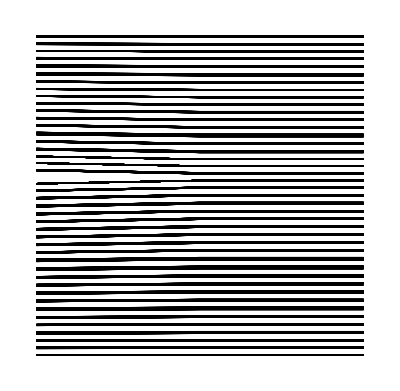

```mathematica
Graphics[plotTimePoint[18,0.02]]
```

```mathematica
poslst=Flatten[clones];
```

```mathematica
Length@res
```

93

```mathematica
res = Take[res,{50,70}];
```

```mathematica
flow2=Graphics[Table[plotTimePoint[i,0.02],{i,1,(Length@res)-1}],AspectRatio->1/(2 N@GoldenRatio),Axes->True,AxesOrigin->{-22,0},Ticks->{Table[{-i,ToString[Length[res]-2-i]},{i,1,Length[res]}],{0,1}} ,ImageSize->800,LabelStyle->Directive[Medium,Bold,FontFamily->"Futura"]];
```